```mathematica
ClearAll["Global`*"]
```

```mathematica
a=0.2;
b=0.1;
```

```mathematica
L=1.243457513715507;
```

```mathematica
f[l_]:={0.5+a Cos[2π l/L](1-Sin[2π l/L]),0.5+ b Sin[2 π l/L](1+Cos[2 π l/L])}
```

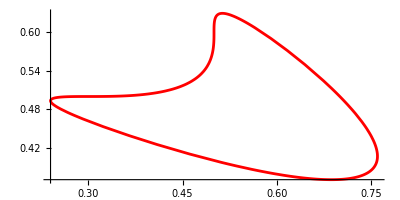

```mathematica
plotcont=ParametricPlot[f[l],{l,0,L},PlotStyle->Red]
```

```mathematica
g[x_]:=x[[1]]+2x[[2]]
```

```mathematica
Integrate[g[f[t]],{t,0,1}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {{{1.19683,1.65703},{1.18128,1.6427},{1.24346,1.7},{1.21237,1.67135},{1.22791,1.68568},{1.11911,1.54435},{1.13465,1.57235},{1.1502,1.60035},«35»,{0.279778,1.66867},{0.295321,1.63634},{0.808247,1.28086},{0.823791,1.28731},{0.839334,1.29376},{0.854877,1.30029},{0.373037,1.47957},«30»},0,1}.

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/check.csv"]
```

{{:0,:1},{0.7,0.5},{0.631433,0.560291},{0.566698,0.606331},{0.522451,0.628455},{0.503025,0.624495},{0.5,0.6},{0.496975,0.565716},{0.477549,0.533349},{0.433302,0.511226},{0.368567,0.501512},{0.3,0.5},{0.25101,0.498488},{0.243091,0.488774},{0.287337,0.466651},{0.379418,0.434284},{0.5,0.4},{0.620582,0.375505},{0.712663,0.371545},{0.756909,0.393669},{0.74899,0.439709}}

```mathematica
t=Table[{t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

{{0.7,0.5},{0.631433,0.560291},{0.566698,0.606331},{0.522451,0.628455},{0.503025,0.624495},{0.5,0.6},{0.496975,0.565716},{0.477549,0.533349},{0.433302,0.511226},{0.368567,0.501512},{0.3,0.5},{0.25101,0.498488},{0.243091,0.488774},{0.287337,0.466651},{0.379418,0.434284},{0.5,0.4},{0.620582,0.375505},{0.712663,0.371545},{0.756909,0.393669},{0.74899,0.439709}}

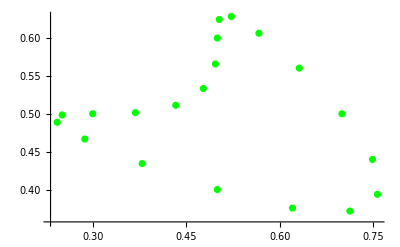

```mathematica
plotdis=ListPlot[t,PlotStyle->Green]
```

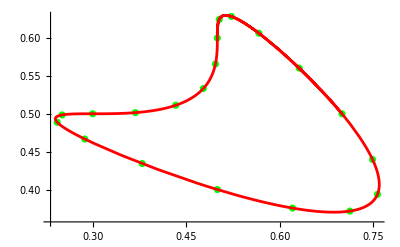

```mathematica
Show[plotdis,plotcont]
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_0_1_on_1.csv"];
t= Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

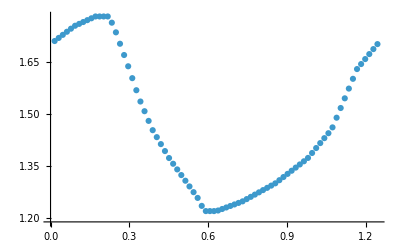

```mathematica
plotdisc=ListPlot[t]
```

```mathematica
u01[x_]:=x[[1]]+2*x[[2]]
```

```mathematica
f[0]
```

{0.7,0.5}

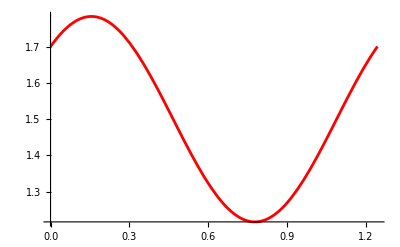

```mathematica
plotcont=Plot[u01[f[l]],{l,0,L},PlotStyle->Red]
```

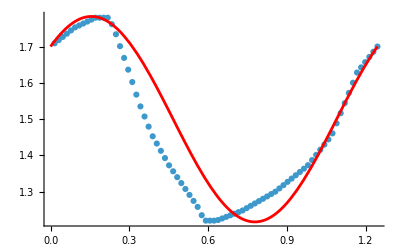

```mathematica
Show[plotdisc,plotcont,PlotRange->Automatic]
```

```mathematica
,
```